# 2味道系统drag force

```mathematica
α=0.2573
```

0.2573

```mathematica
ClearAll
```

ClearAll

```mathematica
A[z_]:=(1/2) Log[2.94 Sin[1.24 Sin[0.47 z+1.94]-9.55]+3.53]
```

```mathematica
T[zh_,μ_]:=1/(π zh)(1-1/2*μ^2 zh^2)
```

```mathematica
AS[z_]:=(1/2) Log[2.94 Sin[1.24 Sin[0.47 z+1.94]-9.55]+3.53]
```

```mathematica
g[z_,zh_,μ_]:=1-(1/zh^4+μ^2/zh^4)z^4+ μ^4/zh^4 z^6
```

```mathematica
T1[zh_]:=1/(π zh)(1-1/2*0^2 zh^2)
```

```mathematica
g1[z_,zh_]:=1-(1/zh^4+0^2/zh^4)z^4+ 0^4/zh^4 z^6
```

```mathematica
FindRoot[T1[zh6]==0.17*1.1,{zh6,1}]
```

```mathematica
zh6=1.7021919047261533
```

1.70219

```mathematica
m1=1.3;m2=4.7
```

4.7

```mathematica
v2[zs_]:=√g1[zs,zh6]
```

```mathematica
p1[zs_]:=(m1*v2[zs])/(√(1-(v2[zs])^2))
```

```mathematica
E1[zs_]:=(α*v2[zs]*Exp[2*AS[zs]])/(2π*zs^2)
```

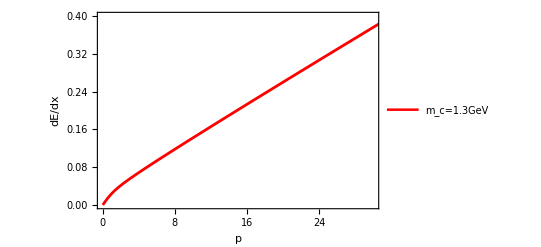

```mathematica
x1=ListLinePlot[ParallelTable[{Re[p1[zs]],Re[E1[zs]]},{zs,0.1,3,0.01}],PlotRange->{{0,30},{0.00001,0.4}},Frame->True,PlotStyle->{{Red,Thickness[0.005]}},BaseStyle->{Black,FontSize->20},PlotLegends->Placed[LineLegend[{"m_c=1.3GeV"},LabelStyle->{FontSize->15}],{0.2,0.9}],FrameLabel->{Style["p",20,Black,Italic],Style["dE/dx",20,Black,Italic]}]
```

```mathematica
p2[zs_]:=(m2*v2[zs])/(√(1-(v2[zs])^2))
```

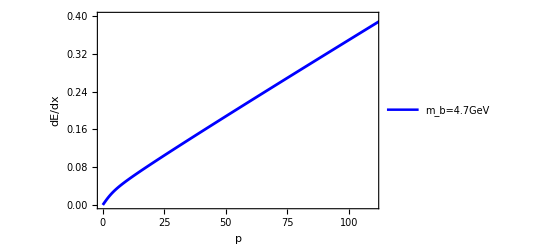

```mathematica
x2=ListLinePlot[ParallelTable[{Re[p2[zs]],Re[E1[zs]]},{zs,0.1,3,0.01}],PlotRange->{{0,110},{0.00001,0.4}},Frame->True,PlotStyle->{{Blue,Thickness[0.005]}},BaseStyle->{Black,FontSize->20},PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(m\), \(b\)]\)=4.7GeV"},LabelStyle->{FontSize->15}],{0.2,0.8}],FrameLabel->{Style["p",20,Black,Italic],Style["dE/dx",20,Black,Italic]}]
```

```mathematica
x5=ListLinePlot[ParallelTable[{Re[x],Re[y[x]]},{x,0.1,3,0.01}],Frame->True,PlotStyle->{{White,Thickness[0.005]}},PlotRange->{{0,15},{0,3}},BaseStyle->{Black,FontSize->20},PlotLegends->Placed[LineLegend[{"T=1.1T_c"},LabelStyle->{FontSize->15}],{0.2,0.7}],FrameLabel->{Style["p",20,Black,Italic],Style["dE/dx",20,Black,Italic]}]
```

-Graphics-

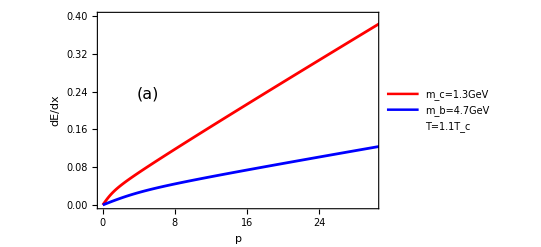

```mathematica
y1=Show[x1,x2,x5,ImageSize->400,Epilog->{Text[Style["(a)",FontFamily->"Times New Roman",FontSize->16],{5,0.22},{Center,Bottom}]},PlotLegends->Placed[LineLegend[{"x1","x2","x5"},LegendMarkerSize->16,LegendLabel->Style["Legend",FontFamily->"Times New Roman",FontSize->16]],{0.8,0.8}],BaseStyle->{FontFamily->"Times New Roman",FontSize->16},AxesStyle->Directive[FontFamily->"Times New Roman",FontSize->16],ImageSize->{500,300}]
```

```mathematica
FindRoot[T1[zh7]==0.17*2,{zh7,1}]
```

{zh7→0.936206}

```mathematica
zh7=0.9362055475993842
```

0.936206

```mathematica
v3[zs_]:=√g1[zs,zh7]
```

```mathematica
p3[zs_]:=(m1*v3[zs])/(√(1-(v3[zs])^2))
```

```mathematica
E2[zs_]:=(α*v3[zs]*Exp[2*AS[zs]])/(2π*zs^2)
```

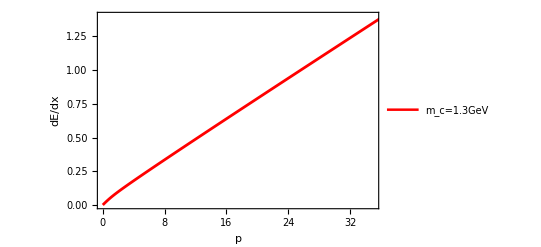

```mathematica
x3=ListLinePlot[ParallelTable[{Re[p3[zs]],Re[E2[zs]]},{zs,0.1,3,0.01}],PlotRange->{{0,35},{0.00001,1.4}},Frame->True,PlotStyle->{{Red,Thickness[0.005]}},PlotRange->{{0,35},{0,1.4}},BaseStyle->{Black,FontSize->20},PlotLegends->Placed[LineLegend[{"m_c=1.3GeV"},LabelStyle->{FontSize->15}],{0.2,0.9}],FrameLabel->{Style["p",20,Black,Italic],Style["dE/dx",20,Black,Italic]}]
```

```mathematica
p4[zs_]:=(m2*v3[zs])/(√(1-(v3[zs])^2))
```

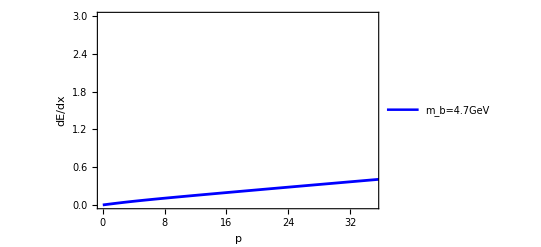

```mathematica
x4=ListLinePlot[ParallelTable[{Re[p4[zs]],Re[E2[zs]]},{zs,0.1,3,0.01}],PlotRange->{{0,35},{0.00001,3}},Frame->True,PlotStyle->{{Blue,Thickness[0.005]}},PlotRange->{{0,35},{0,3}},BaseStyle->{Black,FontSize->20},PlotLegends->Placed[LineLegend[{"m_b=4.7GeV"},LabelStyle->{FontSize->15}],{0.2,0.8}],FrameLabel->{Style["p",20,Black,Italic],Style["dE/dx",20,Black,Italic]}]
```

```mathematica
x6=ListLinePlot[ParallelTable[{Re[x],Re[y[x]]},{x,0.1,3,0.01}],Frame->True,PlotStyle->{{White,Thickness[0.005]}},PlotRange->{{0,35},{0,2.5}},BaseStyle->{Black,FontSize->20},PlotLegends->Placed[LineLegend[{"T=2T_c"},LabelStyle->{FontSize->15}],{0.2,0.7}],FrameLabel->{Style["p",20,Black,Italic],Style["dE/dx",20,Black,Italic]}]
```

-Graphics-

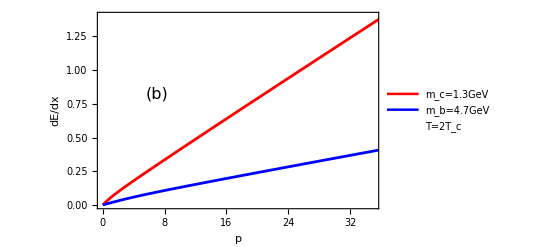

```mathematica
y2=Show[x3,x4,x6,ImageSize->400,Epilog->{Text[Style["(b)",FontFamily->"Times New Roman",FontSize->16],{7,0.77},{Center,Bottom}]},PlotLegends->Placed[LineLegend[{"x1","x2","x5"},LegendMarkerSize->16,LegendLabel->Style["Legend",FontFamily->"Times New Roman",FontSize->16]],{0.8,0.8}],BaseStyle->{FontFamily->"Times New Roman",FontSize->16},AxesStyle->Directive[FontFamily->"Times New Roman",FontSize->16],ImageSize->{500,300}]
```

```mathematica
`
```

NIntegrate::nlim: x = zh5 不是积分的一个有效的极限.

General::stop: 在本次计算中，NIntegrate::nlim 的进一步输出将被抑制.